```mathematica
sigz={{1,0},{0,-1}}
```

{{1,0},{0,-1}}

```mathematica
externalfield=-KroneckerProduct[KroneckerProduct[sigz,id2],id2]-KroneckerProduct[KroneckerProduct[id2,sigz],id2]-2KroneckerProduct[KroneckerProduct[id2,id2],sigz]
```

{{-4,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,-2,0,0,0,0,0},{0,0,0,2,0,0,0,0},{0,0,0,0,-2,0,0,0},{0,0,0,0,0,2,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,4}}

```mathematica
id2=IdentityMatrix[2]
```

{{1,0},{0,1}}

```mathematica
spincoupling=KroneckerProduct[KroneckerProduct[sigz,sigz],id2]+2KroneckerProduct[KroneckerProduct[sigz,id2],sigz]+2KroneckerProduct[KroneckerProduct[id2,sigz],sigz]
```

{{5,0,0,0,0,0,0,0},{0,-3,0,0,0,0,0,0},{0,0,-1,0,0,0,0,0},{0,0,0,-1,0,0,0,0},{0,0,0,0,-1,0,0,0},{0,0,0,0,0,-1,0,0},{0,0,0,0,0,0,-3,0},{0,0,0,0,0,0,0,5}}

```mathematica
hf=externalfield+spincoupling
```

{{1,0,0,0,0,0,0,0},{0,-3,0,0,0,0,0,0},{0,0,-3,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,-3,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,-3,0},{0,0,0,0,0,0,0,9}}

```mathematica
MatrixForm[hf]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -3 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -3 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -3 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -3 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 9)

```mathematica
u=MatrixExp[I hf t]//MatrixForm
```

(ⅇ^(ⅈ t) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | ⅇ^(-3 ⅈ t) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | ⅇ^(-3 ⅈ t) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | ⅇ^(ⅈ t) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ⅇ^(-3 ⅈ t) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ⅇ^(ⅈ t) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(-3 ⅈ t) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(9 ⅈ t))

```mathematica
Eigenvalues[hf]
```

{9,-3,-3,-3,-3,1,1,1}

```mathematica
Eigenvectors[hf]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
htotal[s_]:=(1-s)hinitial+s hf
```

```mathematica
hinitial=b (KroneckerProduct[KroneckerProduct[sigx,id2],id2]+KroneckerProduct[KroneckerProduct[id2,sigx],id2]+KroneckerProduct[KroneckerProduct[id2,id2],sigx])
```

{{0,b,b,0,b,0,0,0},{b,0,0,b,0,b,0,0},{b,0,0,b,0,0,b,0},{0,b,b,0,0,0,0,b},{b,0,0,0,0,b,b,0},{0,b,0,0,b,0,0,b},{0,0,b,0,b,0,0,b},{0,0,0,b,0,b,b,0}}

```mathematica
sigx={{0,1},{1,0}}
```

{{0,1},{1,0}}

```mathematica
MatrixForm[hinitial]
```

(0 | b | b | 0 | b | 0 | 0 | 0
b | 0 | 0 | b | 0 | b | 0 | 0
b | 0 | 0 | b | 0 | 0 | b | 0
0 | b | b | 0 | 0 | 0 | 0 | b
b | 0 | 0 | 0 | 0 | b | b | 0
0 | b | 0 | 0 | b | 0 | 0 | b
0 | 0 | b | 0 | b | 0 | 0 | b
0 | 0 | 0 | b | 0 | b | b | 0)

```mathematica
(1-s)hinitial+s hf
```

{{s,b (1-s),b (1-s),0,b (1-s),0,0,0},{b (1-s),-3 s,0,b (1-s),0,b (1-s),0,0},{b (1-s),0,-3 s,b (1-s),0,0,b (1-s),0},{0,b (1-s),b (1-s),s,0,0,0,b (1-s)},{b (1-s),0,0,0,-3 s,b (1-s),b (1-s),0},{0,b (1-s),0,0,b (1-s),s,0,b (1-s)},{0,0,b (1-s),0,b (1-s),0,-3 s,b (1-s)},{0,0,0,b (1-s),0,b (1-s),b (1-s),9 s}}

```mathematica
Clear[htotal]
```

```mathematica
htotal[s]
```

{{s,b (1-s),b (1-s),0,b (1-s),0,0,0},{b (1-s),-3 s,0,b (1-s),0,b (1-s),0,0},{b (1-s),0,-3 s,b (1-s),0,0,b (1-s),0},{0,b (1-s),b (1-s),s,0,0,0,b (1-s)},{b (1-s),0,0,0,-3 s,b (1-s),b (1-s),0},{0,b (1-s),0,0,b (1-s),s,0,b (1-s)},{0,0,b (1-s),0,b (1-s),0,-3 s,b (1-s)},{0,0,0,b (1-s),0,b (1-s),b (1-s),9 s}}

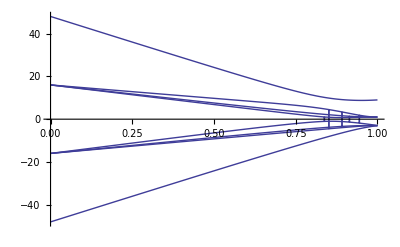

```mathematica
Plot[Eigenvalues[htotal[s]],{s,0,1}]
```

```mathematica
b=16
```

16

```mathematica
Eigenvalues[htotal[1]]
```

{9,-3,-3,-3,-3,1,1,1}

```mathematica
Eigenvalues[htotal[0]]
```

{-48,48,-16,-16,-16,16,16,16}

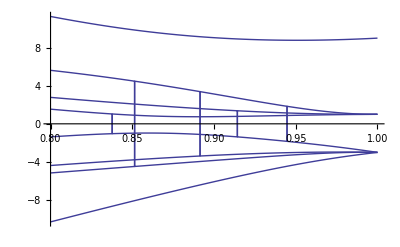

```mathematica
Plot[Eigenvalues[htotal[s]],{s,0.80,1}]
```

```mathematica
htotal[0.914]//MatrixForm
```

(0.914 | 1.376 | 1.376 | 0. | 1.376 | 0. | 0. | 0.
1.376 | -2.742 | 0. | 1.376 | 0. | 1.376 | 0. | 0.
1.376 | 0. | -2.742 | 1.376 | 0. | 0. | 1.376 | 0.
0. | 1.376 | 1.376 | 0.914 | 0. | 0. | 0. | 1.376
1.376 | 0. | 0. | 0. | -2.742 | 1.376 | 1.376 | 0.
0. | 1.376 | 0. | 0. | 1.376 | 0.914 | 0. | 1.376
0. | 0. | 1.376 | 0. | 1.376 | 0. | -2.742 | 1.376
0. | 0. | 0. | 1.376 | 0. | 1.376 | 1.376 | 8.226)

```mathematica
Manipulate[Eigenvalues[htotal[s]],{s,.91,.92}]
```

```mathematica
(* cnot with 4 qubits *)
```

```mathematica
externalfieldc=KroneckerProduct[KroneckerProduct[KroneckerProduct[sigz,id2],id2],id2]+KroneckerProduct[KroneckerProduct[KroneckerProduct[id2,sigz],id2],id2]+KroneckerProduct[KroneckerProduct[KroneckerProduct[id2,id2],sigz],id2]+4KroneckerProduct[KroneckerProduct[KroneckerProduct[id2,id2],id2],sigz]
```

{{7,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,-3,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,5,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,-3,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,3,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,-5,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,-3,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,3,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,-5,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,3,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,-5,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-7}}

```mathematica
spincouplingc=2KroneckerProduct[KroneckerProduct[KroneckerProduct[sigz,sigz],id2],id2]-2KroneckerProduct[KroneckerProduct[KroneckerProduct[sigz,id2],sigz],id2]-4KroneckerProduct[KroneckerProduct[KroneckerProduct[sigz,id2],id2],sigz]-2KroneckerProduct[KroneckerProduct[KroneckerProduct[id2,sigz],sigz],id2]-4KroneckerProduct[KroneckerProduct[KroneckerProduct[id2,sigz],id2],sigz]+4KroneckerProduct[KroneckerProduct[KroneckerProduct[id2,id2],sigz],sigz]
```

{{-6,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,-6,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,18,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,-6,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,-6,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,-6,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,-6,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,18,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,-6,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-6}}

```mathematica
hfc=externalfieldc+spincouplingc
```

{{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,15,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,7,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,-9,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,-3,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,-3,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,7,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,-9,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,-3,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,-3,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,21,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,-11,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-13}}

```mathematica
Eigenvalues[hfc]
```

{21,15,-13,-11,-9,-9,7,7,-3,-3,-3,-3,3,-1,1,1}

```mathematica
Eigenvectors[hfc]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)